```mathematica
UNET`$Verbose=True;
<<UNET`
```

## Generated Data

### Show 2D UNET

```mathematica
dim={112,112};
chan=2;
class=4;
feat=8;
```

```mathematica
MakeUNET[chan,class,feat,dim,DropOutRate->.5,BlockType->"UNET"]
```

```mathematica
MakeUNET[chan,class,feat,dim,DropOutRate->.5,BlockType->"UResNet"]
```

```mathematica
MakeUNET[chan,class,feat,dim,DropOutRate->.5,BlockType->"ResNet"]
```

```mathematica
MakeUNET[chan,class,feat,dim,DropOutRate->.5,BlockType->"UDenseNet"]
```

```mathematica
MakeUNET[chan,class,feat,dim,DropOutRate->.5,BlockType->"DenseNet"]
```

### Show 3D UNET

```mathematica
dim={32,112,112};
chan=2;
class=4;
feat=8;
```

```mathematica
MakeUNET[chan,class,feat,dim,DropOutRate->.5,BlockType->"UNET"]
```

```mathematica
MakeUNET[chan,class,feat,dim,DropOutRate->.5,BlockType->"UResNet"]
```

```mathematica
MakeUNET[chan,class,feat,dim,DropOutRate->.5,BlockType->"ResNet"]
```

```mathematica
MakeUNET[chan,class,{feat,1},dim,DropOutRate->.5,BlockType->"UDenseNet"]
```

```mathematica
MakeUNET[chan,class,{feat,1},dim,DropOutRate->.5,BlockType->"DenseNet"]
```

### Describe UNET

```mathematica
(*general*) 
nets={"Unet", "UResNet", "ResNet", "UDenseNet", "DenseNet"};
style={Bold,TextAlignment->Center,FontFamily->"Helvetica"};
lab=Style[#,style]&/@Join[{"features"},nets];
CountConv=Count[Head/@Information[#,"LayersList"],ConvolutionLayer]&;

(*parameters*)
dim3D={32,96,96};
dim2D=Drop[dim3D,1];
{nchan,nclass}={2,8};

dep={2,4,8,16,24,32};
par=Table[ToString[dep[[i]]],{i,1,Length[dep]}];
```

```mathematica
(*2D UNET generation*)
par2D=Table[
nets2D=MakeUNET[nchan,nclass, dep[[i]], dim2D, BlockType-># ]&/@nets;
Flatten@{par[[i]],Information[#,"ArraysTotalElementCount"]&/@nets2D}
,{i,1,Length[dep]}];
layers2D=ToString[CountConv[#]]&/@nets2D;
```

```mathematica
(*3D UNET generation*)
par3D=Table[
nets3D=MakeUNET[nchan,nclass, dep[[i]],dim3D,BlockType-># ]&/@nets;
Flatten@{par[[i]],Information[#,"ArraysTotalElementCount"]&/@nets3D}
,{i,1,Length[dep]}];
layers3D=ToString[CountConv[#]]&/@nets3D;
```

```mathematica
(*make Table*)
layers=Column[{Style["Number of convolution layers",style],Style["1)  UNet: "<>layers2D[[1]]<>"    2)  UResNet: "<>layers2D[[2]]<>
"    3)  ResNet: "<>layers2D[[3]]<>"    4)  UDenseNet: "<>layers2D[[4]]<>"    5)  DenseNet: "<>layers2D[[5]],style]},Alignment->Center];
tab1=Column[{Style["2D Nets - Numer of Array Elementes",style],
TableForm[par2D,TableHeadings->{None,lab},TableAlignments->Right]},Alignment->Center];
tab2=Column[{Style["3D Nets - Numer of Array Elementes",style],
TableForm[par3D,TableHeadings->{None,lab},TableAlignments->Right]},Alignment->Center];

Column[{layers,"",tab1,"",tab2},Alignment->Center]
```

Number of convolution layers
1)  UNet: 24    2)  UResNet: 24    3)  ResNet: 33    4)  UDenseNet: 40    5)  DenseNet: 83

2D Nets - Numer of Array Elementes
features | Unet | UResNet | ResNet | UDenseNet | DenseNet
2 | 29400 | 15364 | 17188 | 1802 | 2752
4 | 115376 | 59692 | 66068 | 6364 | 9304
8 | 457080 | 235264 | 258928 | 23792 | 33832
16 | 1819496 | 934072 | 1025048 | 91864 | 128584
24 | 4087256 | 2096432 | 2298368 | 204224 | 284264
32 | 7260360 | 3722344 | 4078888 | 360872 | 500872

3D Nets - Numer of Array Elementes
features | Unet | UResNet | ResNet | UDenseNet | DenseNet
2 | 84624 | 42976 | 44800 | 4538 | 5200
4 | 336272 | 170140 | 176516 | 17308 | 19096
8 | 1340664 | 677056 | 700720 | 67568 | 73000
16 | 5353832 | 2701240 | 2792216 | 266968 | 285256
24 | 12039512 | 6072560 | 6274496 | 598208 | 636776
32 | 21397704 | 10791016 | 11147560 | 1061288 | 1127560

### Examples of Test Data

```mathematica
{data,label}=CreateImage1[];
Flatten@{MakeChannelImage[data],Image[label]}
```

```mathematica
{data,label}=CreateImage2[];
Flatten@{MakeChannelImage[data],MakeClassImage[label]}
```

```mathematica
{data,label}=CreateImage3[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

```mathematica
{data,label}=CreateImage4[];
Flatten@{MakeChannelImage[data],MakeClassImage[label,{1,4}]}
```

### Test Cases 1: 1 channel - 1 classes

```mathematica
(*make test data*)
{data1,label1}=MakeTestImages[100,1];
```

```mathematica
(*split the data*)
{train1,valid1,testData1,testLabel1,order1}=SplitTrainData[data1,label1];
```

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

Number of Samples in each set: {70,20,10}

```mathematica
(*train the net*)
{{net1,trained1,netTrained1},{result1,iou1}}=TrainUNET[train1,valid1,{testData1,testLabel1},
TargetDevice->{"GPU",1},MaxTrainingRounds->250,NetParameters->2,DropOutRate->.5,BatchSize->32];
MakeNetPlots[trained1]
```

channels: 1 - classes: 1 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.978}

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData1,netTrained1]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->False]
```

```mathematica
(*visualize the test data with diff image*)
ShowChannelClassData[testData1,testLabel1,result1, NumberRowItems->3,MakeDifferenceImage->True]
```

### Test Case 2: 1 channel - 2 classes

```mathematica
(*make test data*)
{data2,label2}=MakeTestImages[100,2];
```

```mathematica
(*split the data*)
{train2,valid2,testData2,testLabel2,order}=SplitTrainData[data2,label2];
```

Dimensions data: {100,1,128,128} - Dimensions label: {100,128,128}

Number of Samples in each set: {70,20,10}

```mathematica
(*train the net*)
{{net2,trained2,netTrained2},{result2,iou2}}=TrainUNET[train2,valid2,{testData2,testLabel2},BatchSize->32,
TargetDevice->{"GPU",1},MaxTrainingRounds->250,DropOutRate->0.5,NetParameters->2,
AugmentTrainData->{False,False,True}];
MakeNetPlots[trained2]
```

channels: 1 - classes: 2 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.998,2→0.987}

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData2,netTrained2]
```

```mathematica
Options[ShowChannelClassData]
```

{ImageSize→500,ClassScale→Automatic,NumberRowItems→3,MakeDifferenceImage→False,ClassStepSize→1,AspectRatio→1}

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData2, testLabel2,result2, NumberRowItems->3,MakeDifferenceImage->True,ClassStepSize->1]
```

### Test Case 3: 1 channel - 4 classes

```mathematica
(*make test data*)
{data3,label3}=MakeTestImages[200,3];
```

```mathematica
(*split the data*)
{train3,valid3,testData3,testLabel3,order3}=SplitTrainData[data3,label3];
```

Dimensions data: {200,1,128,128} - Dimensions label: {200,128,128}

Number of Samples in each set: {140,40,20}

channels: 1 - classes: 4 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→1.,2→0.855,3→0.913,4→0.997}

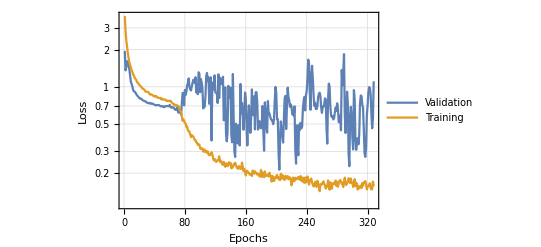
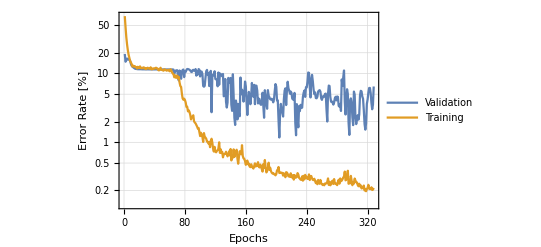

```mathematica
(*train the net*)
{{net3,trained3,netTrained3},{result3,iou3}}=TrainUNET[train3,valid3,{testData3,testLabel3},BatchSize->32,
TargetDevice->{"GPU",1},MaxTrainingRounds->500,DropOutRate->0.5,NetParameters->16,
AugmentTrainData->{"90",False,True}];
MakeNetPlots[trained3]
```

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData3,netTrained3]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData3, testLabel3, result3, NumberRowItems->3,
MakeDifferenceImage->True,ClassStepSize->1]
```

### Test Case 4 : 3 channels - 4 classes

```mathematica
(*make test data*)
{data4,label4}=MakeTestImages[100,4];
```

```mathematica
(*split the data*)
{train4,valid4,testData4,testLabel4,order4}=SplitTrainData[data4,label4];
```

Dimensions data: {100,3,128,128} - Dimensions label: {100,128,128}

Number of Samples in each set: {70,20,10}

```mathematica
(*train the net*)
{{net4,trained4,netTrained4},{result4,iou4}}=TrainUNET[train4,valid4,{testData4,testLabel4},
BatchSize->32,
TargetDevice->{"GPU",1},MaxTrainingRounds->200,NetParameters->16,
DropOutRate->0.5,AugmentTrainData->{"90",False,True}];
MakeNetPlots[trained4]
```

channels: 3 - classes: 4 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→1.,2→0.999,3→1.,4→0.996}

```mathematica
(*visualize the layers of the net*)
VisualizeUNET2D[testData4,netTrained4]
```

```mathematica
(*visualize the test data with diff image*)
ShowChannelClassData[testData4, testLabel4,NumberRowItems->2,MakeDifferenceImage->True]
```

```mathematica
(*visualize the validation data with diff image*)
ShowChannelClassData[valid4[[;;9,1]],valid4[[;;9,2]],ClassDecoder[netTrained4[valid4[[1;;9,1]],TargetDevice->"GPU"],4],
 NumberRowItems->2,MakeDifferenceImage->True]
```

### Test Case 5 - same as 4 with animation

```mathematica
{data5,label5}=MakeTestImages[100,4];
```

```mathematica
{train5,valid5,testData5,testLabel5,order}=SplitTrainData[data5,label5];
```

Dimensions data: {100,3,128,128} - Dimensions label: {100,128,128}

Number of Samples in each set: {70,20,10}

```mathematica
(*choose a nice image*)
MakeChannelImage/@testData5
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
im=6;nchan=Max[testLabel5];solutions={};
imChan=First@MakeChannelImage[testData5[[im,{1}]]];
(*The monitoring function*)
monitor=AppendTo[solutions,ClassDecoder[NetExtract[#Net,"net"][testData5[[im]],TargetDevice->"GPU"],nchan]]&;
```

channels: 3 - classes: 4 - Dimensions :{128,128}

Evaluating test data

DICE per class: {1→0.995,2→0.867,3→0.999,4→0.058}

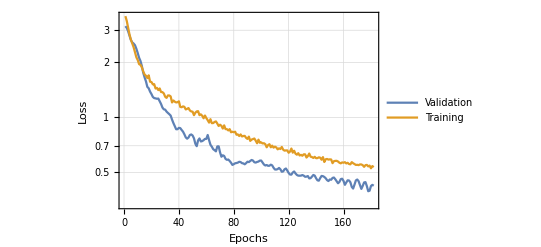
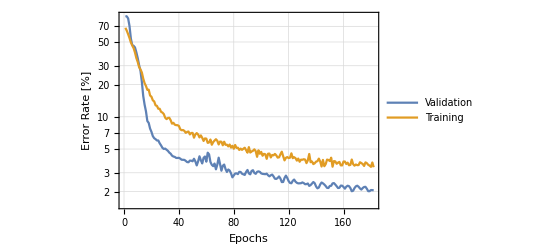

```mathematica
(*train the net with monitor function*)
{{net,trained,netTrained},{result,iou}}=TrainUNET[train5,valid5,{testData5,testLabel5},BatchSize->35,
 TargetDevice->{"GPU",1},MaxTrainingRounds->200,NetParameters->16,DropOutRate->.5,NetLossLayers->All,
AugmentTrainData->{"90",False,True},
TrainingProgressFunction->{monitor,"Interval"->Quantity[1,"Rounds"]}];
MakeNetPlots[trained]
```

```mathematica
(*visualize the test data witout diff image*)
ShowChannelClassData[testData5, testLabel5, result, NumberRowItems->2,MakeDifferenceImage->True,ClassStepSize->1,ImageSize->650]
```

```mathematica
(*make the animation images*)
solIm=ColorReplace[MakeClassImage[#,{1,4}],ColorData["Rainbow"][0]]&/@solutions;
anim=Table[Show[ImageCompose[imChan,{sol,.5}],ImageSize->500],{sol,solIm}];

(*play the animatin*)
Animate[im,{im,anim}]
```

```mathematica
Export["anim-v2.gif",anim,"DisplayDuration"->.2,"AnimationRepetitions"->Infinity]
```